```mathematica
<<NDSolve`FEM`
```

# Solution of the Stokes equation.

## Defining geometry of the domain

```mathematica
b={x-1/2,x+1/2,y-1/2,y+1/2,(x-1/2)^2+(y-1/2)^2-0.3^2,(x+1/2)^2+(y+1/2)^2-0.3^2,(x-1/2)^2+(y+1/2)^2-0.3^2,(x+1/2)^2+(y-1/2)^2-0.3^2};
```

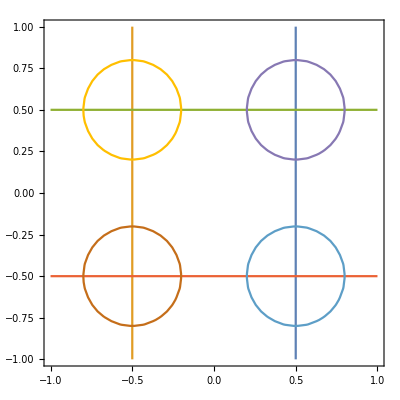

```mathematica
ContourPlot[Evaluate[(#==0&/@b)],{x,-1,1},{y,-1,1},Contours->{0}]
```

```mathematica
Ω=ImplicitRegion[!((x-1/2)^2+(y-1/2)^2≤0.3^2||(x+1/2)^2+(y+1/2)^2≤0.3^2||(x-1/2)^2+(y+1/2)^2≤0.3^2||(x+1/2)^2+(y-1/2)^2≤0.3^2),{{x,-1/2,1/2},{y,-1/2,1/2}}];
```

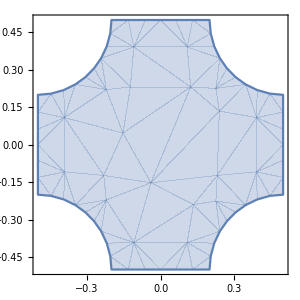

```mathematica
RegionPlot[Ω,AspectRatio->Automatic,ImageSize->300]
```

## Creating finite element mesh

```mathematica
bΜ=ToBoundaryMesh[Ω,"MaxBoundaryCellMeasure"->0.1]
```

ElementMesh[{{-0.5,0.5},{-0.5,0.5}},Automatic]

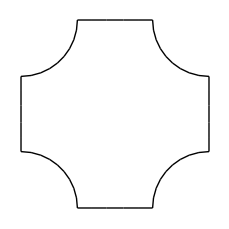

```mathematica
ElementMeshWireframe[bΜ]
```

```mathematica
pointMarkerFunction=Compile[{{coords,_Real,2}},(Block[{x=#1⟦1⟧,y=#1⟦2⟧,epsilon},epsilon=1/10^5.;Which[Abs[x-1/2]≤epsilon,1,Abs[x+1/2]≤epsilon ,2,Abs[y-1/2]≤epsilon,3,Abs[y+1/2]≤epsilon, 4,((x-1/2)^2+(y-1/2)^2-0.3^2≤epsilon ||(x+1/2)^2+(y+1/2)^2-0.3^2≤epsilon||(x-1/2)^2+(y+1/2)^2-0.3^2≤epsilon||(x+1/2)^2+(y-1/2)^2-0.3^2≤epsilon),5,True,0]]&)/@coords];
```

```mathematica
pm=pointMarkerFunction[bΜ["Coordinates"]]
```

{2,2,2,2,2,2,1,1,1,1,1,1,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,3,4,4,4,4,4,4,3,3,3,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

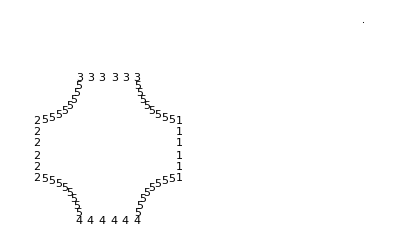

```mathematica
Graphics[{PointSize[0.002],Point[{4/Sqrt[5],2/Sqrt[5]}],MapThread[Text[ToString[#1],#2]&,{pm,bΜ["Coordinates"]}]}]
```

```mathematica
boundaryMarkerFunction=Compile[{{boundaryElementCoords,_Real,3},{boundaryElementPointMarkres,_Integer,2}},Which[Union[#]=={1},1,Union[#]=={2},2,Union[#]=={3},3,Union[#]=={4},4,True,5]&/@boundaryElementPointMarkres];
```

```mathematica
bΜ=ToBoundaryMesh[Ω,"PointMarkerFunction"->pointMarkerFunction,"BoundaryMarkerFunction"->boundaryMarkerFunction,"MaxBoundaryCellMeasure"->0.1,"BoundaryMeshGenerator"->"RegionPlot","RegionHoles"->None]
```

ElementMesh[{{-0.5,0.5},{-0.5,0.5}},Automatic]

```mathematica
bΜ["BoundaryElements"]
```

{LineElement[{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{22,23},{23,24},{24,25},{25,26},{26,27},{27,28},{28,29},{29,30},{30,31},{31,32},{32,33},{33,34},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,42},{42,43},{43,44},{44,45},{45,46},{46,47},{47,48},{48,49},{49,50},{50,1}},{4,4,5,5,5,5,5,5,5,5,2,2,2,2,5,5,5,5,5,5,5,5,3,3,3,3,5,5,5,5,5,5,5,5,1,1,1,1,5,5,5,5,5,5,5,5,4,4,4,4}]}

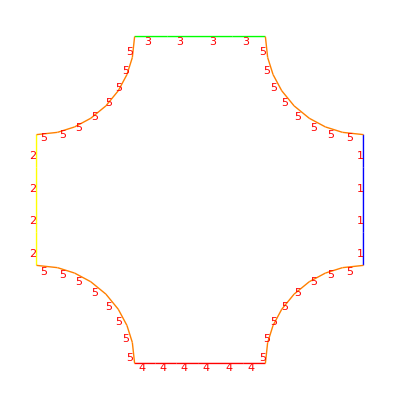

```mathematica
bΜ["Wireframe"["MeshElementMarkerStyle"->Red,"MeshElementStyle"->{Blue,Yellow,Green,Red,Orange}]]
```

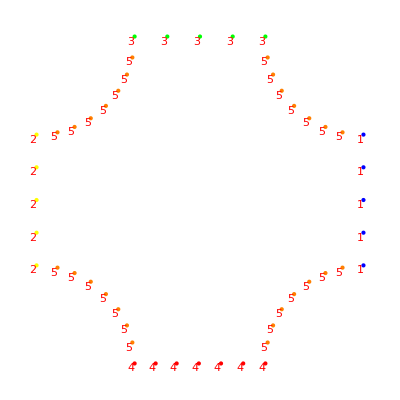

```mathematica
bΜ["Wireframe"["MeshElement"->"PointElements","MeshElementMarkerStyle"->Red,"MeshElementStyle"->{Blue,Yellow,Green,Red,Orange}]]
```

```mathematica
mesh=ToElementMesh[bΜ,"MaxCellMeasure"->0.1]
```

ElementMesh[{{-0.5,0.5},{-0.5,0.5}},{TriangleElement[<152>]}]

```mathematica
Union[Join@@ElementMarkers[mesh["BoundaryElements"]]]
```

{1,2,3,4,5}

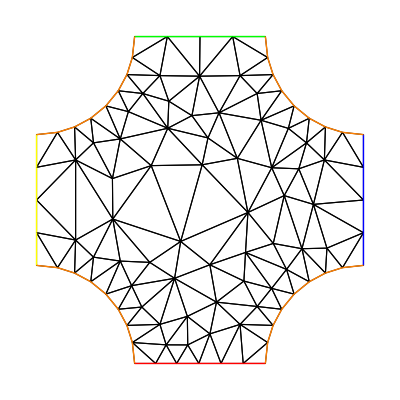

```mathematica
Show[mesh["Wireframe"],mesh["Wireframe"["MeshElement"->"BoundaryElements","MeshElementStyle"->{Blue,Yellow,Green,Red,Orange}]]]
```

```mathematica
Union[Join@@ElementMarkers[mesh["PointElements"]]]
```

{1,2,3,4,5}

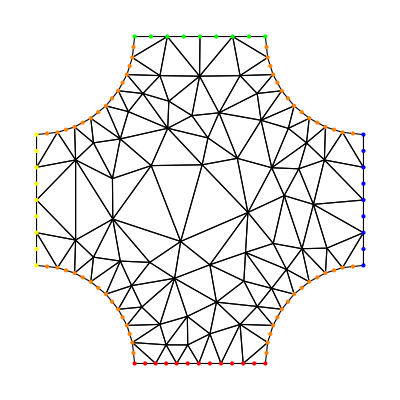

```mathematica
Show[mesh["Wireframe"],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementStyle"->{Blue,Yellow,Green,Red,Orange}]]]
```

```mathematica
ℐ=IdentityMatrix[2];
```

```mathematica
stokesFlowOperator={(ℐ.u[x,y]{x,y}Inactive){x,y}Inactive+Derivative[1,0][w][x,y],(ℐ.v[x,y]{x,y}Inactive){x,y}Inactive+Derivative[0,1][w][x,y],Derivative[0,1][v][x,y]+Derivative[1,0][u][x,y]};
```

```mathematica
bΜ["Wireframe"["MeshElement"->"PointElements","MeshElementMarkerStyle"->Red,"MeshElementStyle"->{Blue,Yellow,Green,Red,Orange}]]
```

-Graphics-

## Defining boundary conditions

```mathematica
Subscript[Γ, D]={DirichletCondition[{w[x,y]==1},ElementMarker==1],
DirichletCondition[{w[x,y]==0},ElementMarker==2],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},ElementMarker==3],
DirichletCondition[{u[x,y]==0.,v[x,y]==0.},ElementMarker==4],
DirichletCondition[{u[x,y]==0.,v[x,y]==0.},ElementMarker==5]};
```

## Solution of the equation

```mathematica
{xVel,yVel,pressure}=NDSolveValue[{stokesFlowOperator=={0,0,0},Subscript[Γ, D]},{u,v,w},{x,y}∈mesh,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,w->2}}];
```

## Plot the equation

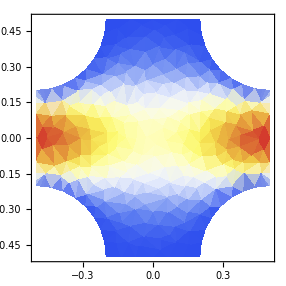

```mathematica
DensityPlot[Sqrt[xVel[x,y]^2+yVel[x,y]^2],{x,y}∈mesh,AspectRatio->Automatic,ColorFunction->"TemperatureMap"]
```

InterpolatingFunction::dmval: Input value {-0.5, -0.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

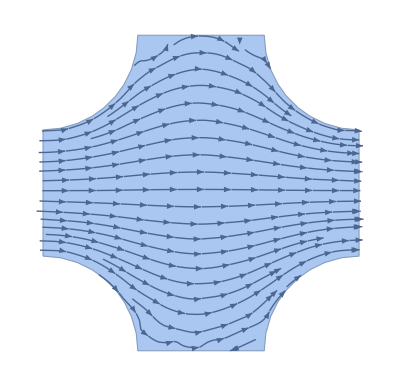

```mathematica
Show[BoundaryDiscretizeRegion[Ω],StreamPlot[{xVel[x,y],yVel[x,y]},{x,y}∈mesh,AspectRatio->Automatic]]
```